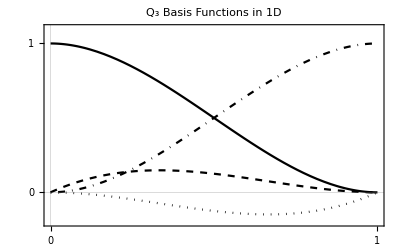

```mathematica
plt=Plot[{1-3 x^2+2 x^3,x-2 x^2+x^3,-(x^2-x^3),3 x^2-2 x^3},{x,0,1},PlotStyle->{{Black},{Black,Dashed},{Black,Dotted},{Black,DotDashed}},PlotLabel->"Q_3 Basis Functions in 1D",FrameTicks->{{{{0,0},{0.2,},{0.4,},{0.6,},{0.8,},{1,1}},{}},{{{0,0},{0.2,},{0.4,},{0.6,},{0.8,},{1,1}},{}}},PlotRange->{-0.2,1.1}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["../figures/hermite.pdf",plt]
```

../figures/hermite.pdf